```mathematica
Clear["f12","f22","f32"]
```

```mathematica
expl = {f1->(x0-k1 x1)/(a1 + b1 x0 + c1 x1),
f2->(x1-k2 x2)/(a2 + b2 x1 + c2 x2),
f3->(x2-k3 x3)/(a3 + b3 x2 + c3 x3)};
Dexpl = {f11->D[f1/.expl,x0],f12->-D[f1/.expl,x1],
f21->D[f2/.expl,x1],f22->-D[f2/.expl,x2],
f31->D[f3/.expl,x2],f32->-D[f3/.expl,x3]};
```

```mathematica
rules = {f22->c2 f2 f21}
DC = {1- f3/f1 f12/f21 f22/f21, f2/f1 f12/f21 - f3/f1 f12/f21 f22/f21};
DE = {f2o f3o/(f1o f3o + f2o f3o + f1o f2o),f1o f3o/(f1o f3o + f2o f3o + f1o f2o)} - {f2 f3/(f1 f3 + f2 f3 + f1 f2),f1 f3/(f1 f3 + f2 f3 + f1 f2)};
DC . DE // FullSimplify
DC . DE /.rules// FullSimplify
DC . DE/.expl //Simplify
```

{f22→c2 f2 f21}

(f1o f2o f3 (-f1 f2 f21 (f12+f21)+f12 (f1+f2) f22 f3)+(f12 f1o f2^2 f21 f3+f1^2 f21^2 f2o (f2+f3)+f1 f2 (f12 f1o f2 f21-(f1o (f21^2+f12 f22)+f12 (f21+f22) f2o) f3)) f3o)/(f1 f21^2 (f2 f3+f1 (f2+f3)) (f2o f3o+f1o (f2o+f3o)))

(f1o f2 f2o f3 (-f1 (f12+f21)+c2 f12 (f1+f2) f3)+(f12 f1o f2^2 f3+f1^2 f21 f2o (f2+f3)+f1 f2 (f12 f1o f2-(f1o f21+f12 f2o+c2 f12 f2 (f1o+f2o)) f3)) f3o)/(f1 f21 (f2 f3+f1 (f2+f3)) (f2o f3o+f1o (f2o+f3o)))

-((f12 (a1+b1 x0+c1 x1) (f21 (x1-k2 x2) (a3+b3 x2+c3 x3)-f22 (a2+b2 x1+c2 x2) (x2-k3 x3)) ((f2o f3o+f1o (f2o+f3o)) (x0-k1 x1) (a2+b2 x1+c2 x2) (x2-k3 x3)-f1o f3o ((x0-k1 x1) (x1-k2 x2) (a3+b3 x2+c3 x3)+(x0-k1 x1) (a2+b2 x1+c2 x2) (x2-k3 x3)+(a1+b1 x0+c1 x1) (x1-k2 x2) (x2-k3 x3)))+(a2+b2 x1+c2 x2) (f21^2 (x0-k1 x1) (a3+b3 x2+c3 x3)-f12 f22 (a1+b1 x0+c1 x1) (x2-k3 x3)) ((f2o f3o+f1o (f2o+f3o)) (a1+b1 x0+c1 x1) (x1-k2 x2) (x2-k3 x3)-f2o f3o ((x0-k1 x1) (x1-k2 x2) (a3+b3 x2+c3 x3)+(x0-k1 x1) (a2+b2 x1+c2 x2) (x2-k3 x3)+(a1+b1 x0+c1 x1) (x1-k2 x2) (x2-k3 x3))))/(f21^2 (f2o f3o+f1o (f2o+f3o)) (x0-k1 x1) (a2+b2 x1+c2 x2) (a3+b3 x2+c3 x3) ((x0-k1 x1) (x1-k2 x2) (a3+b3 x2+c3 x3)+(x0-k1 x1) (a2+b2 x1+c2 x2) (x2-k3 x3)+(a1+b1 x0+c1 x1) (x1-k2 x2) (x2-k3 x3))))

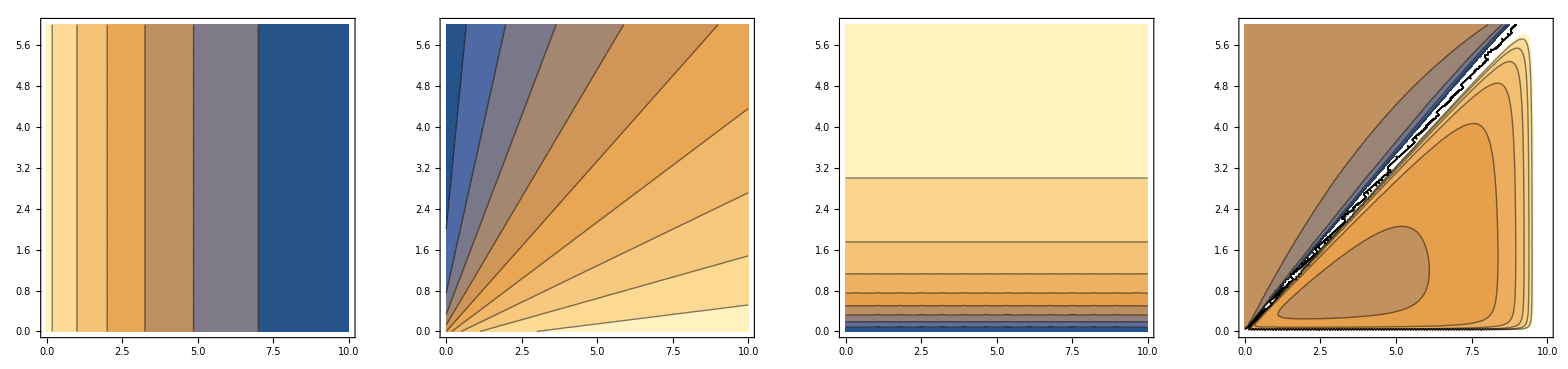

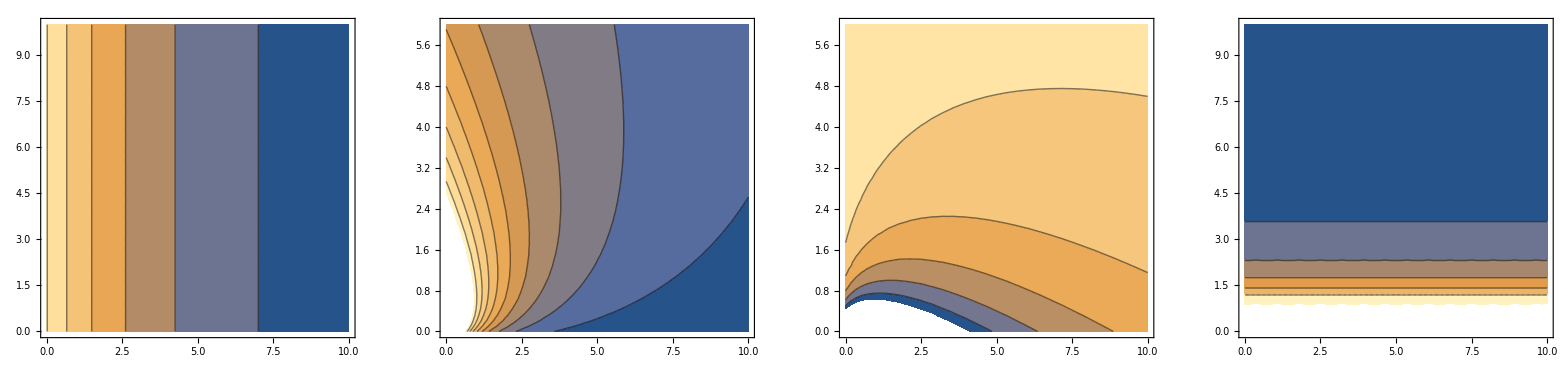

```mathematica
pars={
k1->1, a1->2,b1->3,c1->4,
k2->1.5, a2->1.5,b2->2,c2->3,
k3->.5, a3->3,b3->4,c3->2,
x0->10,x3->0};
p1=ContourPlot[{f1}/.expl/.pars,{x1,0,10},{x2,0,6}];
p2=ContourPlot[f2/.expl/.pars,{x1,0,10},{x2,0,6}];
p3=ContourPlot[f3/.expl/.pars,{x1,0,10},{x2,0,6}];
p4=ContourPlot[1/f1+1/f2+1/f3/.expl/.pars,{x1,0,10},{x2,0,6}];
pd12=ContourPlot[(4 (10-x1))/(32+4 x1)^2+1/(32+4 x1),{x1,0,10},{x2,0,10}];
pd21=ContourPlot[-(2 (x1-1.5 x2))/(1.5+2 x1+3 x2)^2+1/(1.5+2 x1+3 x2),{x1,0,10},{x2,0,6}];
pd22=ContourPlot[-(3 (x1-1.5 x2))/(1.5+2 x1+3 x2)^2-1.5/(1.5+2 x1+3 x2),{x1,0,10},{x2,0,6}];
pd31=ContourPlot[-(4 (0.+x2))/(3+4 x2)^2+1/(3+4 x2),{x1,0,10},{x2,0,10}];
GraphicsRow[{p1,p2,p3,p4}]
GraphicsRow[{pd12,pd21,pd22,pd31}]
```

```mathematica
D[f3/.expl/.pars,x2]
```

-(4 (0.+x2))/(3+4 x2)^2+1/(3+4 x2)

```mathematica
ContourPlot[f2/.expl/.pars,{x1,0,10},{x2,0,10}]
```

-Graphics-